# Experiment Data Processing

## Mean Information Gain

## Implementation

### Functions

```mathematica
pcond[{data_,initial_String,direction_String,neighbor_String}]:=Module[{result},(Length@Select[#,MatchQ[#[[1]],initial]&])/Length[#]&@Select[data,MatchQ[#,{_,direction,neighbor}]&]];
```

```mathematica
pneighbor[{data_,initial_String,direction_String}]:=(Length@Select[data,MatchQ[#,{_,direction,initial}]&])/(Length@Select[data,MatchQ[#,{_,direction,_}]&]);
```

```mathematica
p[{data_,initial_String,direction_String,neighbor_String}]:=pneighbor[{data,neighbor,direction}]*pcond[{data,initial,direction,neighbor}];
```

```mathematica
IGMEQ[data_List,direction_String]:=Total[Flatten@Quiet[
N@Table[-p[{data,i,direction,j}]*Log[2,pcond[{data,i,direction,j}]],
{i,{"0","1"}},{j,{"0","1"}}]
,{Infinity::indet,Power::infy}]/.Indeterminate:>0];
```

```mathematica
IGMCounter[m_List]:=Module[{result,right,left,down,up},
right=Join@@StringCases[StringJoin/@IntegerString[m],x_~~y_:>{x,"right",y},Overlaps->True];
left=Join@@StringCases[StringJoin/@IntegerString[m],y_~~x_:>{x,"left",y},Overlaps->True];
down=Join@@StringCases[StringJoin/@IntegerString[Transpose[m]],x_~~y_:>{x,"down",y},Overlaps->True];
up=Join@@StringCases[StringJoin/@IntegerString[Transpose[m]],y_~~x_:>{x,"up",y},Overlaps->True];
result=Join@@{right,left,down,up}
];
```

```mathematica
SymmetricInformationGainModel[CA_List]:=Module[{data,result},
(*Print[ArrayPlot[CA,Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny]];*)
data=IGMCounter[CA];
result=IGMEQ[data,#]&/@{"up","down","right","left"};
Thread[Rule[{Subscript[G, up],Subscript[G, down],Subscript[G, right],Subscript[G, left]},result]]
]
```

### Examples

```mathematica
r1=SymmetricInformationGainModel[{{0,0,0},{0,1,0},{0,0,0}}]
```

{G_up→0.601607,G_down→0.601607,G_right→0.601607,G_left→0.601607}

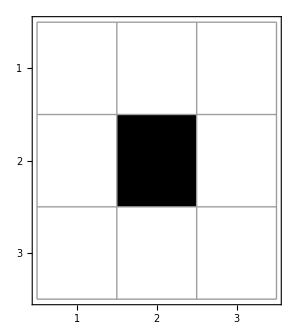

```mathematica
c1=ArrayPlot[{{0,0,0},{0,1,0},{0,0,0}},Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny]
```

```mathematica
r2=SymmetricInformationGainModel[{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}}]
```

{G_up→0.,G_down→0.,G_right→0.,G_left→0.}

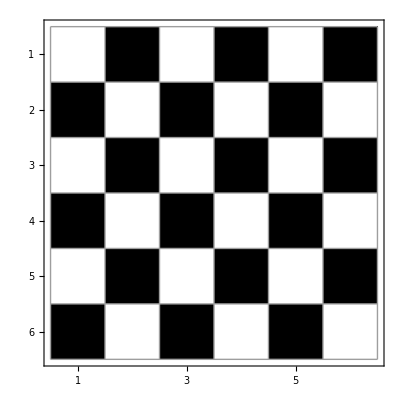

```mathematica
c2=ArrayPlot[{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}},Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny]
```

```mathematica
SymmetricInformationGainModel[{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}]
```

{G_up→0.550978,G_down→0.550978,G_right→0.,G_left→0.}

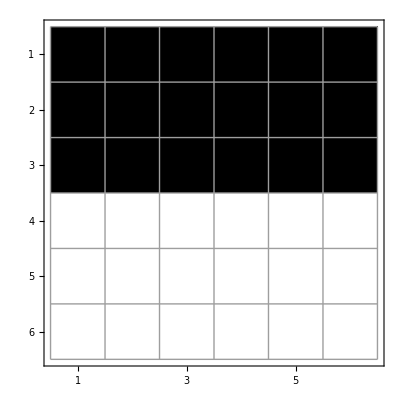

```mathematica
c2=ArrayPlot[{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny]
```

```mathematica
SymmetricInformationGainModel[Transpose@{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}]
```

{G_up→0.,G_down→0.,G_right→0.550978,G_left→0.550978}

```mathematica
SymmetricInformationGainModel[{{0,1,0,0,0,1},{1,1,0,1,0,1},{0,1,0,0,1,0},{0,0,1,0,0,1},{1,1,1,1,0,1},{0,0,1,0,1,1}}]
```

{G_up→0.983871,G_down→0.987079,G_right→0.93766,G_left→0.947314}

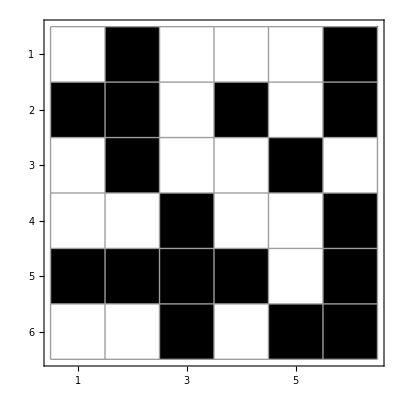

```mathematica
ArrayPlot[{{0,1,0,0,0,1},{1,1,0,1,0,1},{0,1,0,0,1,0},{0,0,1,0,0,1},{1,1,1,1,0,1},{0,0,1,0,1,1}},Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny]
```

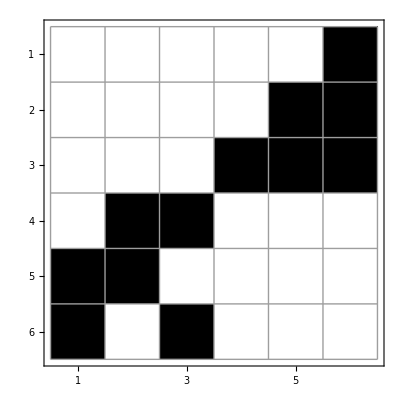

```mathematica
Print[ArrayPlot[{{0,0,0,0,0,1},{0,0,0,0,1,1},{0,0,0,1,1,1},{0,1,1,0,0,0},{1,1,0,0,0,0},{1,0,1,0,0,0}},Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny]]
```

```mathematica
SymmetricInformationGainModel[{{0,0,0,0,0,1},{0,0,0,0,1,1},{0,0,0,1,1,1},{0,1,1,0,0,0},{1,1,0,0,0,0},{1,0,1,0,0,0}}]
```

{G_up→0.920861,G_down→0.891078,G_right→0.814619,G_left→0.851624}

```mathematica
ArrayPlot[{{0,0,0,0,0,1},{0,0,0,0,1,1},{0,0,0,1,1,1},{0,1,1,0,0,0},{1,1,0,0,0,0},{1,0,1,0,0,0}},Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny]
```

-Graphics-

### Images

```mathematica
cases={
{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}},{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},
{{0,1,0,0,0,1},{1,1,0,1,0,1},{0,1,0,0,1,0},{0,0,1,0,0,1},{1,1,1,1,0,1},{0,0,1,0,1,1}}};
```

```mathematica
g=Dataset[<|#|>]&/@(SymmetricInformationGainModel[#]&/@cases)
```

{,,}

```mathematica
gplots=ArrayPlot[#,Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny]&/@cases
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[gplots->g]
```

{-Graphics-→,-Graphics-→,-Graphics-→}

```mathematica
Dataset[<|Thread[gplots->g]|>,Alignment->Baseline]
```

```mathematica
Dataset[<|(ArrayPlot[#,Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny]-><|SymmetricInformationGainModel[#]|>)&/@cases|>,Alignment->{Baseline,Baseline},HeaderAlignment->{Left,Baseline},HeaderSize->{Automatic,0.8}]
```

```mathematica
Column[Labeled[ArrayPlot[#,Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny],SymmetricInformationGainModel[#]]&/@cases,Center,Frame->True,Background->{White,LightBlue}]
```

-Graphics-{G_up→0.,G_down→0.,G_right→0.,G_left→0.}
-Graphics-{G_up→0.550978,G_down→0.550978,G_right→0.,G_left→0.}
-Graphics-{G_up→0.983871,G_down→0.987079,G_right→0.93766,G_left→0.947314}

```mathematica
Canvas[c2]
```

```mathematica
img=-Graphics-;
```

```mathematica
Show[img,PlotLabel->P(white|Subscript[black, up])=6/18]
```

-Graphics-

P(white|black_up)

```mathematica
Labeled[ArrayPlot[{{0,0,0},{0,1,0},{0,0,0}},Mesh->True,Frame->True,FrameTicks->All,ImageSize->Tiny],]
```

```mathematica
Gup
```

(Ḡ)_up (Ḡ)_down
(Ḡ)_left (Ḡ)_right

## Experiments

## Static system

### MIG: 100 experiments with 50 agents

#### Cleaning data

```mathematica
NotebookDirectory[]
```

C:\Users\sebas\Desktop\Documentos\Github\QuantifyingEmergenceMIG\

```mathematica
StaticDataRaw=Import[NotebookDirectory[]<>"Data\\modelo_convergente_100.csv","Data"];
```

```mathematica
StaticDataRaw[[7]]
```

{[run number],[step],matrix:to-row-list M}

```mathematica
StaticDataRaw[[4]]
```

{07/14/2025 22:00:09:481 -0500}

```mathematica
StaticData=MapAt[ToExpression@StringReplace[#,{"["->"{","]"->"}",WhitespaceCharacter->","}]&,StaticDataRaw[[8;;]],{All,3}];//AbsoluteTiming
```

{118.555,Null}

```mathematica
ExperimentStaticData=SortBy[#,#[[2]]&]&/@GatherBy[StaticData,First];
```

```mathematica
ExperimentStaticData2=#[[-1000;;]]&/@ExperimentStaticData;
```

```mathematica
ResultPerRunStaticData=MapAt[SymmetricInformationGainModel,ExperimentStaticData2,{All,All,3}];//AbsoluteTiming
```

{974.864,Null}

```mathematica
Export[NotebookDirectory[]<>"Data\\modelo_convergente_100_1.m",ResultPerRunStaticData];
```

```mathematica
ResultPerRunStaticData=Import[NotebookDirectory[]<>"Data\\modelo_convergente_100_1.m"];
```

```mathematica
StatisticsStaticData=Transpose[Normal[GroupBy[Join@@ResultPerRunStaticData[[All,All,{2,3}]],First,Around[Mean[#],StandardDeviation[#]]&/@Values[Transpose[#[[All,2]]]]&]][[All,2]]];//AbsoluteTiming
```

{0.407476,Null}

```mathematica
StatisticsStaticData[[1,1]]
```

0.120.09

#### Results

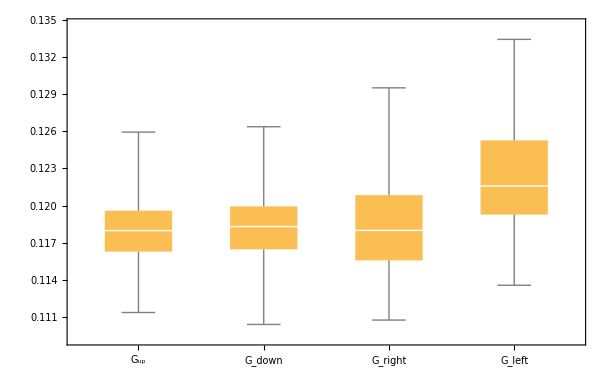

```mathematica
BoxWhiskerChart[Transpose[Map[Mean,Values[Transpose[ResultPerRunStaticData[[All,All,3]]]]]],ChartLabels->{"G_up","G_down","G_right","G_left"}]
```

## Periodic system

### MIG: 100 experiments with 50 agents

#### Cleaning data

```mathematica
PeriodicDataRaw=Import[NotebookDirectory[]<>"Data\\modelo_periodico_100.csv","Data"];
```

```mathematica
PeriodicDataRaw[[7]]
```

{[run number],[step],matrix:to-row-list M}

```mathematica
PeriodicData=MapAt[ToExpression@StringReplace[#,{"["->"{","]"->"}",WhitespaceCharacter->","}]&,PeriodicDataRaw[[8;;]],{All,3}];
```

```mathematica
ExperimentPeriodicData=SortBy[#,#[[2]]&]&/@GatherBy[PeriodicData,First];
```

```mathematica
Length@ExperimentPeriodicData[[1]]
```

1001

```mathematica
ResultPerRunPeriodicData=MapAt[SymmetricInformationGainModel,ExperimentPeriodicData,{All,All,3}];//AbsoluteTiming
```

{917.668,Null}

```mathematica
Export[NotebookDirectory[]<>"Data\\modelo_periodic_100.m",ResultPerRunPeriodicData];
```

```mathematica
ResultPerRunPeriodicData=Import[NotebookDirectory[]<>"Data\\modelo_periodic_100.m"];
```

```mathematica
StatisticsPeriodicData=Transpose[Normal[GroupBy[Join@@ResultPerRunPeriodicData[[All,All,{2,3}]],First,Around[Mean[#],StandardDeviation[#]]&/@Values[Transpose[#[[All,2]]]]&]][[All,2]]];//AbsoluteTiming
```

{0.352752,Null}

#### Result

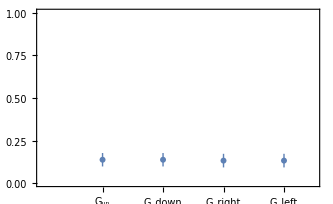

```mathematica
ListPlot[Around[Mean[#],StandardDeviation[#]]&/@Transpose[Map[Mean[#]&,Values[Transpose[ResultPerRunPeriodicData[[All,All,3]]]]]],PlotRange->{{0,4.5},{0,1}},Frame->True,FrameTicks->{{All,None},{{{1,"G_up"},{2,"G_down"},{3,"G_right"},{4,"G_left"}},None}}]
```

### Position SD per experiment

#### Cleaning data

```mathematica
PeriodicDataRaw=Import[NotebookDirectory[]<>"Data\\modelo_periodico_1000.csv","Data"];//AbsoluteTiming
```

{0.371298,Null}

```mathematica
ExperimentPeriodicData=SortBy[#,#[[2]]&]&/@GatherBy[PeriodicDataRaw[[8;;]],First];//AbsoluteTiming
```

{0.0019232,Null}

To count last pair of standard deviation of each experiment:

```mathematica
CountPeriodicData=Count[ExperimentPeriodicData[[All,-1,{-2,-1}]],#]&/@{{0,0},{Except[0],Except[0]},{0,Except[0]},{Except[0],0}};//AbsoluteTiming
```

{0.000589,Null}

#### Result

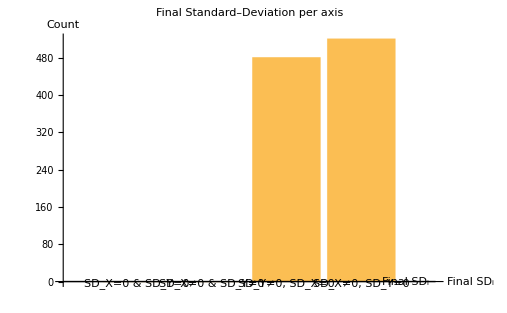

```mathematica
BarChart[CountPeriodicData,ChartLabels->{"SD_X=0 & SD_Y=0","SD_X≠0 & SD_Y≠0","SD_Y≠0, SD_X=0","SD_X≠0, SD_Y=0"},AxesLabel->{"Final SD_i","Count"},PlotLabel->"Final Standard–Deviation per axis"]
```

## Complex system

### 100 experiments with 50 agents

#### Cleaning data

```mathematica
ComplexDataRaw=Import[NotebookDirectory[]<>"Data\\modelo_complejo_100.csv","Data"];
```

```mathematica
ComplexData=MapAt[ToExpression@StringReplace[#,{"["->"{","]"->"}",WhitespaceCharacter->","}]&,ComplexDataRaw[[8;;]],{All,3}];
```

```mathematica
ExperimentComplexData=SortBy[#,#[[2]]&]&/@GatherBy[ComplexData,First];
```

```mathematica
ResultPerRunComplexData=MapAt[SymmetricInformationGainModel,ExperimentComplexData,{All,All,3}];//AbsoluteTiming
```

{910.072,Null}

```mathematica
Export[NotebookDirectory[]<>"Data\\modelo_complejo_100.m",ResultPerRunComplexData];
```

```mathematica
ResultPerRunComplexData=Import[NotebookDirectory[]<>"Data\\modelo_complejo_100.m"];
```

```mathematica
StatisticsComplexData=Transpose[Normal[GroupBy[Join@@ResultPerRunComplexData[[All,All,{2,3}]],First,Around[Mean[#],StandardDeviation[#]]&/@Values[Transpose[#[[All,2]]]]&]][[All,2]]];//AbsoluteTiming
```

{0.385988,Null}

#### Results

Results evidence that the system tend to be have high entropy in every direction:

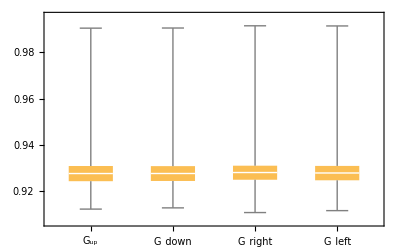

```mathematica
BoxWhiskerChart[Transpose[Map[Mean,Values[Transpose[ResultPerRunComplexData[[All,All,3]]]]]],ChartLabels->{"G_up","G_down","G_right","G_left"}]
```

```mathematica
Grid[Partition[Table[
ArrayPlot[ExperimentComplexData2[[1,All,3]][[i]],Mesh->True,Frame->True,FrameTicksStyle->5,ImageSize->Tiny,ColorRules->{0->Gray,1->White},"FrameLabel"->"t = "<>ToString@(i-1)],
{i,1,250,30}],UpTo[3]]]
```

-Graphics-

```mathematica
Grid[Partition[Table[
ArrayPlot[ExperimentComplexData2[[1,All,3]][[i]],Mesh->True,Frame->True,FrameTicksStyle->5,ImageSize->Tiny,ColorRules->{0->Gray,1->White},"FrameLabel"->"t = "<>ToString@(i-1)],
{i,1,5001,250}],UpTo[7]]]
```

-Graphics-

## Chaotic system

### 100 experiments with 50 agents

#### Cleaning data

```mathematica
ChaoticDataRaw=Import[NotebookDirectory[]<>"Data\\modelo_caotico_100.csv","Data"];
```

```mathematica
ChaoticData=MapAt[ToExpression@StringReplace[#,{"["->"{","]"->"}",WhitespaceCharacter->","}]&,ChaoticDataRaw[[8;;]],{All,3}];
```

```mathematica
ExperimentChaoticData=SortBy[#,#[[2]]&]&/@GatherBy[ChaoticData,First];
```

```mathematica
Length@ExperimentChaoticData[[1]]
```

1001

```mathematica
ResultPerRunChaoticData=MapAt[SymmetricInformationGainModel,ExperimentChaoticData,{All,All,3}];//AbsoluteTiming
```

{908.438,Null}

```mathematica
Export[NotebookDirectory[]<>"Data\\modelo_caotico_100.m",ResultPerRunChaoticData];
```

```mathematica
ResultPerRunChaoticData=Import[NotebookDirectory[]<>"Data\\modelo_caotico_100.m"];
```

```mathematica
StatisticsChaoticData=Transpose[Normal[GroupBy[Join@@ResultPerRunChaoticData[[All,All,{2,3}]],First,Around[Mean[#],StandardDeviation[#]]&/@Values[Transpose[#[[All,2]]]]&]][[All,2]]];//AbsoluteTiming
```

{0.452931,Null}

#### Results

Results evidence that the system tend to be chaotic in every direction:

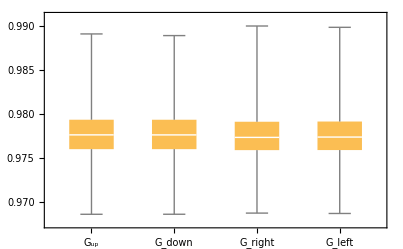

```mathematica
BoxWhiskerChart[Transpose[Map[Mean,Values[Transpose[ResultPerRunChaoticData[[All,All,3]]]]]],ChartLabels->{"G_up","G_down","G_right","G_left"}]
```

```mathematica
Grid[Partition[Table[
ArrayPlot[ExperimentChaoticData[[7,All,3]][[i]],Mesh->True,Frame->True,FrameTicksStyle->5,ImageSize->Tiny,ColorRules->{0->Gray,1->White},"FrameLabel"->"t = "<>ToString@(i-1)],
{i,1,1001,50}],UpTo[7]]]
```

-Graphics-